```mathematica
func[x_]:=x
Clear[a]
cE[a_, s_]:= Expectation[func[x]*(x - a), Distributed[x, NormalDistribution[a, s]]]
cV[a_, s_] := Expectation[(func[x] * (x - a) - cE[a, s])^2, Distributed[x, NormalDistribution[a, s]]]
cV[a, s]/s^4
```

(a^2 s^2+2 s^4)/s^4

```mathematica
gradientEstimatePoint[x_] := func[x]*(x - mu)
estimator[X_] := Map[func, X].(X - Table[mu, Length[X]])/(s^2*Length[X])
estimatorCV[X_] := Map[func, X].(X - Table[Mean[X], Length[X]])/(s^2*Length[X]);
numSamples= 50;
cov := s^2*IdentityMatrix[numSamples];
Expectation[estimator[Array[x, numSamples]],Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Expectation[(estimator[Array[x, numSamples]] - 1)^2,Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Expectation[estimatorCV[Array[x, numSamples]],Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Expectation[(estimatorCV[Array[x, numSamples]] - 9/10)^2,Distributed[Array[x,numSamples], MultinormalDistribution[Table[mu, numSamples], cov]]]
Simplify[estimatorCV[Array[x, 5]]]
```

1

(mu^2+2 s^2)/(50 s^2)

49/50

57/1250

1/(25 s^2)(4 x[1]^2+4 x[2]^2+4 x[3]^2-2 x[3] x[4]+4 x[4]^2-2 x[3] x[5]-2 x[4] x[5]+4 x[5]^2-2 x[2] (x[3]+x[4]+x[5])-2 x[1] (x[2]+x[3]+x[4]+x[5]))

```mathematica
meanFun[{1,2,3}]
a = {1,2 , 3};
Total[a] / Length[a]
```

meanFun[{1,2,3}]

2

```mathematica
BetaDistribution
```

```mathematica
{-1,-1}
```

```mathematica
Expectation[x[1]^2 * x[2]^2,
```

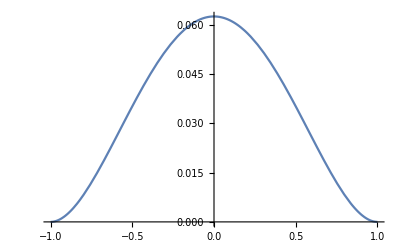

```mathematica
Plot[(x / 2 + 1/2)^2 (1/2 - x/2)^2, {x, -1, 1}]
```

```mathematica
e4 = Simplify[Expectation[(2R(u - 1/2))^4, Distributed[u, BetaDistribution[a, a]]]]
e2=Simplify[Expectation[(2R(u - 1/2))^2, Distributed[u, BetaDistribution[a, a]]]]
```

(3 R^4)/(3+8 a+4 a^2)

R^2/(1+2 a)

```mathematica
v1 = Simplify[2(t - e2)/(e4)]
```

(2 (-1+2 a) (-R^2+(-3+2 a) t))/(3 R^4)

```mathematica
gg = (a - 1)/(2 R^2) (4 (2a - 1)(2a - 3))/((a - 2)(a-1))(t/(2R^2) (a  - 3/2)- 1/4)
v2 = Simplify[gg]
```

(2 (-3+2 a) (-1+2 a) (-1/4+((-3/2+a) t)/(2 R^2)))/((-2+a) R^2)

((-3+2 a) (-1+2 a) (-R^2+(-3+2 a) t))/(2 (-2+a) R^4)

```mathematica
v1 - v2
```

((-1+2 a) (-R^2+(-3+2 a) t))/(6 R^4)-((-1+a) (-1+2 a) (-R^2+(-3+2 a) t))/(a R^4)

```mathematica
Simplify[u^2/(2R^2) (a - 3/2) - 1/4]
```

1/4 (-1+((-3+2 a) u^2)/R^2)

```mathematica
Simplify[(a - 2)/(2R^2) u^2 - (1/4 - u^2/(4R^2))]
```

1/4 (-1+((-3+2 a) u^2)/R^2)

```mathematica
f[x_, x0_, R_, a_] := 1/Beta[a, a] * (1/2 + (x - x0)/(2R))^(a - 1)(1/2 - (x - x0)/(2R))^(a - 1);
Simplify[D[f[x, x0, R, a], {x0}]]
Simplify[D[f[x, x0, R, a], {x0, 2}]]
```

(2^(3-2 a) (-1+a) R^2 (x-x0) (((R+x-x0) (R-x+x0))/R^2)^a)/((R+x-x0)^2 (R-x+x0)^2 Beta[a,a])

(2^(3-2 a) (-1+a) R^2 (-R^2+(-3+2 a) (x-x0)^2) (((R+x-x0) (R-x+x0))/R^2)^a)/((R+x-x0)^3 (R-x+x0)^3 Beta[a,a])

```mathematica
(2^(3-2 a) (-1+a) R^2 (-R^2+(-3+2 a) (x-x0)^2) (((R+x-x0) (R-x+x0))/R^2)^a)/((R+x-x0)^3 (R-x+x0)^3 Beta[a,a])
```

```mathematica
(2^-3 (-1+a) (-R^2+(-3+2 a) (x-x0)^2) (((R+x-x0) (R-x+x0))/(4 R^2))^(a-3))/(R^4 Beta[a,a])
```

```mathematica
(2^-3 (-1+a) (-R^2+(-3+2 a) (x-x0)^2))/(R^4 Beta[a,a])
```

```mathematica
haha = (2^-3 (-1+a) (-R^2+(-3+2 a) (x-x0)^2))/R^4/( (a - 1)(a - 2))^2*((2a - 1)(2a - 2)(2a - 3)(2a - 4))
Simplify[haha]
```

((-4+2 a) (-3+2 a) (-2+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/(8 (-2+a)^2 (-1+a) R^4)

((-3+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/(2 (-2+a) R^4)

```mathematica
(32 (-3+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/((-2+a) R^4)
```

(32 (-3+2 a) (-1+2 a) (-R^2+(-3+2 a) (x-x0)^2))/((-2+a) R^4)

```mathematica
Clear[alpha, a, b, c, d, R, x0]
taylorF[X_] := a  + b(X - x0) + c/2 (X- x0)^2 + d/6 (X - x0)^3;
coordinateBeta[z_] := 2R(z - 1/2) + x0 ;
BetaCentralMoment[N_] := Expectation[(coordinateBeta[z] - x0)^N, Distributed[z, BetaDistribution[alpha, alpha]]]
ApproxGrad= 1/BetaCentralMoment[2] * Expectation[taylorF[coordinateBeta[z]]*(coordinateBeta[z] - x0), Distributed[z, BetaDistribution[alpha, alpha]]];
Simplify[Expectation[(1/BetaCentralMoment[2] * taylorF[coordinateBeta[z]]*(coordinateBeta[z] - x0) - ApproxGrad)^2, Distributed[z, BetaDistribution[alpha, alpha]]]]
```

(12 a^2 (3+2 alpha)^2 (35+94 alpha+52 alpha^2+8 alpha^3)+36 a (105+352 alpha+344 alpha^2+128 alpha^3+16 alpha^4) c R^2+R^2 (384 alpha^4 b^2+945 c^2 R^2+24 alpha^3 (120 b^2+15 c^2 R^2+16 b d R^2)+4 alpha^2 (1704 b^2+495 c^2 R^2+480 b d R^2+32 d^2 R^4)+alpha (5040 b^2+2790 c^2 R^2+2016 b d R^2+208 d^2 R^4)))/(12 (3+2 alpha)^2 (5+2 alpha) (7+2 alpha) R^2)

```mathematica
f[r_, a_] := (1/2)^(2a - 3)* r^(5/2)*1/Beta[a, a]  *(1 + r)^(a - 1)* (1 - r)^(a - 1 - 3 );
inF[a_]:=Integrate[f[r, a], {r, 0, 1}];
```

```mathematica
Plot[inF[a], {a, 10, 100}]
```

```mathematica
D[f[r, a], {r}]
```

(2^(3-2 a) (-1+a) (1-r)^(-4+a) r^(5/2) (1+r)^(-2+a))/Beta[a,a]+(5 2^(2-2 a) (1-r)^(-4+a) r^(3/2) (1+r)^(-1+a))/Beta[a,a]-(2^(3-2 a) (-4+a) (1-r)^(-5+a) r^(5/2) (1+r)^(-1+a))/Beta[a,a]

```mathematica
Expectation[Abs[(x)]^(k), Distributed[x, NormalDistribution[0, a]]]
```

(2^(k/2) a^k Gamma[(1+k)/2])/(√π)

```mathematica
Clear[R]
f[r_] := Log[(R- r)(R
 + r)]
g[r_] =Simplify[D[f[r], {r, 2}]]
```

-(2 (r^2+R^2))/((r-R)^2 (r+R)^2)

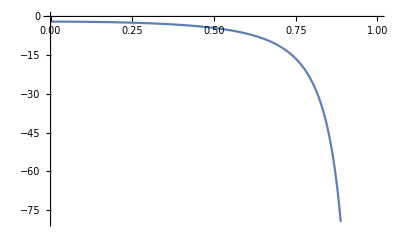

```mathematica
Plot[g[r], {r, 0, 1}]
```

```mathematica
g[0]
```

```mathematica
Simplify[D[f[r], {r, 3}]]
```

(4 (r^3+3 r R^2))/((r-R)^3 (r+R)^3)

```mathematica
Integrate[Abs[x]^k e^{-x^2 / a}, {x, -Infinity, Infinity}]
```

{ConditionalExpression[1/2 (1+(-1)^k) Gamma[(1+k)/2] (Log[e]/a)^(-1/2-k/2),Re[k]>-1&&Re[Log[e]/a]>0]}

```mathematica
Expectation[Abs[x]^k, Distributed[x, NormalDistribution[0, a]]]
```

(2^(k/2) a^k Gamma[(1+k)/2])/(√π)